```mathematica
Needs["PlotLegends`"]
SetDirectory[FileNameJoin[{NotebookDirectory[]}]]
Subscript[η, B]=Last[Flatten[StringSplit[FileNames["ETA_B_*",NotebookDirectory[]],"_"]]];
κσr = Last[Flatten[StringSplit[FileNames["KAPPA_SIGMA_R_*",NotebookDirectory[]],"_"]]];
```

/Users/htailor/Desktop/dna_lite/ksr50/etab_3.0/Analysis

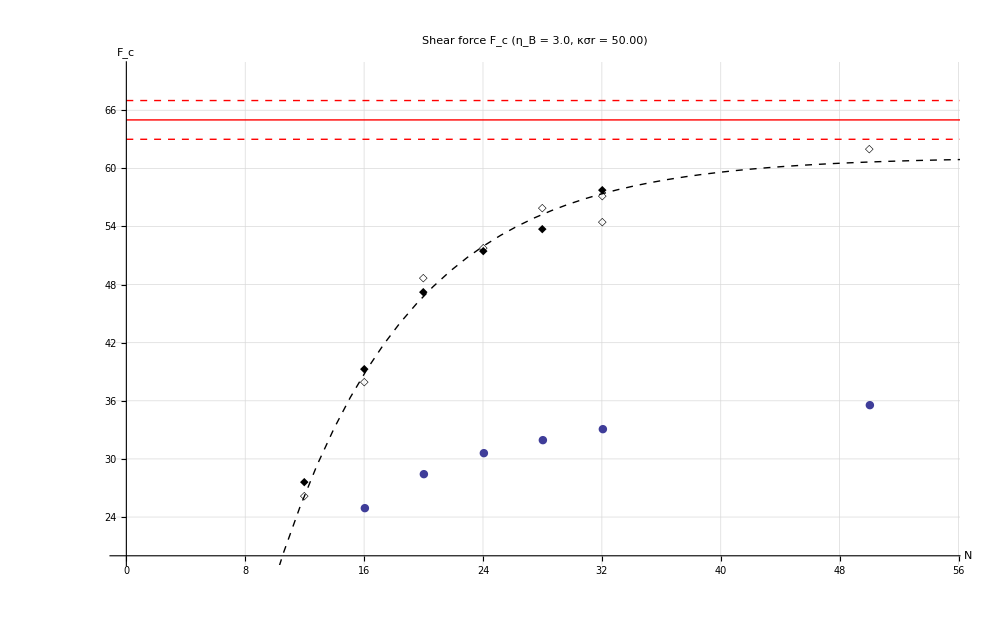

DeGennes Fit (Hatch Data):
-------------------------------------
 f_c = 3.39121 pN	 κσr = 162.683	 shift = 0.684393

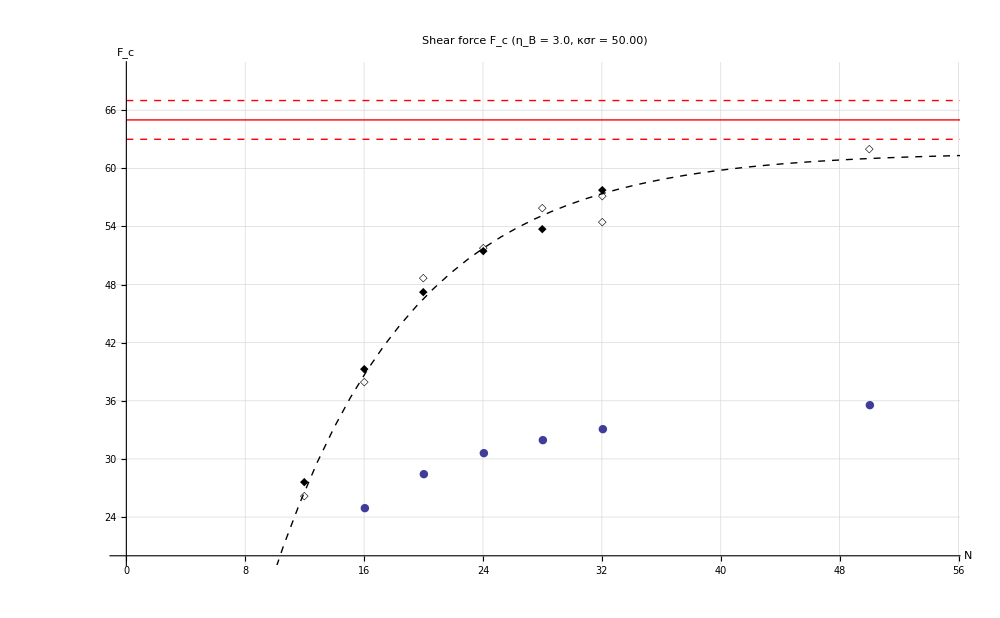

DeGennes Fit (Hatch Data):
-------------------------------------
 f_c = 3.23673 pN	 κσr = 181.462

```mathematica
HatchData33Points=Import["./Hatch_Data/hatch33.dat","Table"];
HatchData55Points=Import["./Hatch_Data/hatch55.dat","Table"];

DataPoints=Transpose[Import["force.data","Table"]];
DataPointsFc=Table[{DataPoints[[1]][[i]],DataPoints[[2]][[i]]},{i,1,Length[DataPoints[[1]]]}];

UpperLevel=Table[{i,67},{i,0,60}];
AsymLevel=Table[{i,65},{i,0,60}];
LowerLevel=Table[{i,63},{i,0,60}];

fsTitle=24;
fsAxesLabel=18;
fs2=16;

Data=ListPlot[{HatchData33Points,HatchData55Points,DataPointsFc},PlotStyle->{{Black,FontSize->18},{Black,FontSize->18},{ColorData[1,1]},{ColorData[1,2]}},PlotMarkers->{"◆","◇","●"}];
AsymLevelData =ListLinePlot[
{
UpperLevel,
AsymLevel,
LowerLevel
},
PlotStyle->{
{Thick,Dashed,Red},
{Thick,Red},
{Thick,Dashed,Red}
}
];
legend={
{Graphics[{Black,Inset[Style["◆",FontSize->18],{0,0}]}],Style["3'3' Data",FontSize->fs2]},
{Graphics[{Black,Inset[Style["◇",FontSize->18],{0,0}]}],Style["5'5' Data",FontSize->fs2]},
{Graphics[{ColorData[1,1],Inset[Style["●",FontSize->16],{0,0}]}],Style["F_c",FontSize->fs2]}
};

(*model1 =(2 Subscript[f, c]) (χ^-1 Tanh[(χ (x-s))/2]+1);*)
(*model1 =2 Subscript[f, c] χ^-1 Tanh[(χ (x-s))/2];*)
model1 =2 Subscript[f, c] χ^-1 (1-2Exp[-χ (x-s)]);

DeGennesfit = FindFit[HatchData55Points,model1,{{Subscript[f, c],3.16},{χ,0.125},s},x];
DeGennesFit=Plot[Evaluate[model1 /. DeGennesfit],{x,5,60},PlotStyle->{Thick,Dashed,Black}];

DeGennesκσr=(χ^2/2)^-1/.DeGennesfit;
Subscript[DeGennesf, c]=Subscript[f, c]/.DeGennesfit;
DeGennesS=s/.DeGennesfit;


ShowLegend[Show[
{
Data,AsymLevelData,DeGennesFit
},
PlotRange->{{0,55},{20,70}},
GridLines->Automatic,
GridLinesStyle->Directive[LightGray,Dashed],
AxesOrigin->{0,20},
AxesLabel->{
Style["N",FontSize->fsAxesLabel],
Style["F_c",FontSize->fsAxesLabel]
},
LabelStyle->{"Times",FontSize->fs2},
PlotLabel->Style["Shear force F_c (η_B = "<>ToString[Subscript[η, B]]<>", κσr = "<>ToString[κσr]<>")",FontSize->fsTitle],
ImageSize->1000
],{legend,LegendShadow->None,
LegendBorder->False,
LegendSize->{0.4,0.15},
LegendPosition->{0.2,-0.4},
LegendBackground->Opacity[0],
ShadowBackground->Opacity[0]}]

Print["\nDeGennes Fit (Hatch Data):\n-------------------------------------\n f_c = ",Subscript[DeGennesf, c] pN,"\t κσr = ",DeGennesκσr,"\t shift = ",DeGennesS];

(*model2 =(2 Subscript[f, c]) (χ^-1 Tanh[(χ x)/2]+1);*)
(*model2 =2 Subscript[f, c] χ^-1 Tanh[(χ x)/2];*)
model2 =2 Subscript[f, c] χ^-1 (1-2Exp[-χ  x]);

DeGennesfit = FindFit[HatchData55Points,model2,{{Subscript[f, c],3.16},{χ,0.125}},x];
DeGennesFit=Plot[Evaluate[model2 /. DeGennesfit],{x,5,60},PlotStyle->{Thick,Dashed,Black}];

DeGennesκσr=(χ^2/2)^-1/.DeGennesfit;
Subscript[DeGennesf, c]=Subscript[f, c]/.DeGennesfit;

ShowLegend[Show[
{
Data,AsymLevelData,DeGennesFit
},
PlotRange->{{0,55},{20,70}},
GridLines->Automatic,
GridLinesStyle->Directive[LightGray,Dashed],
AxesOrigin->{0,20},
AxesLabel->{
Style["N",FontSize->fsAxesLabel],
Style["F_c",FontSize->fsAxesLabel]
},
LabelStyle->{"Times",FontSize->fs2},
PlotLabel->Style["Shear force F_c (η_B = "<>ToString[Subscript[η, B]]<>", κσr = "<>ToString[κσr]<>")",FontSize->fsTitle],
ImageSize->1000
],{legend,LegendShadow->None,
LegendBorder->False,
LegendSize->{0.4,0.15},
LegendPosition->{0.2,-0.4},
LegendBackground->Opacity[0],
ShadowBackground->Opacity[0]}]

Print["\nDeGennes Fit (Hatch Data):\n-------------------------------------\n f_c = ",Subscript[DeGennesf, c] pN,"\t κσr = ",DeGennesκσr];
```